# Introducción a Mathematica

## I. Sistemas de álgebra computacional

### Son programas que permiten la computación sobre expresiones matemáticas de una manera simbólica. Estos programas son usados en campos que van desde matemáticas, ciencias naturales, ingeniería, economía y demás. En particular, muchos cálculos importantes en la física teórica no podrían haber sido calculados a mano y necesitaron de la ayuda del álgebra computacional. Existen diversos programas que pueden ser usados para hacer álgebra computacional, algunos de ellos son: Maple, Mathematica, MATLAB symbolic toolbox, Maxima, entre otros. En los inicios de 1988, un joven físico Steven Wolfram junto con algunos colegas desarrollaron la primera versión de Mathematica.

## II. Cómo escribir

### ■ Notebooks: Es una herramienta en Mathematica que permite escribir diferentes tipos de documentos. Los notebooks serán de ahora en adelante donde escribiremos la información y los códigos que adelantaremos en nuestros proyectos. Para crear un notebook podemos: - En la ventana principal buscar la opción Notebook - Ir a File, New, Notebook ( o teclear Crtl+N )

### ■ Formas de entrada: Mathematica presenta tres formas de escritura básica: Escritura libre, Lenguaje de Mathematica y Escritura de paletas. Desde Mathematica 8 aparece un asistente de inserción al dar click dentro de un notebook o presionando la tecla abajo, el asistente tiene la forma de un signo más y permite escoger la forma entrada. -Graphics- Figura 1: Asistente de inserción El asistente además permite crear estilos de texto como: Títulos, secciones, subsecciones, capítulos y muchos más. Los estilos permiten personalizar los proyectos en los notebooks y hacerlos más organizados.

#### Escritura libre: Permite al usuario escribir en lenguaje cotidiano, en inglés, tal y como piensa. En este tipo de entrada es traducido en los servidores de Mathematica al lenguaje y muestra una respuesta con la opción de desplegar más información dando click en el signo más. Para usar la escritura la escritura libre se debe ir al asistente de inserción dar click sobre la opción “Free-Form input” o simplemente presionar shift+0 (signo igual).

WolframAlphaQueryResults

x==-ⅈ||x==ⅈ

WolframAlphaQueryParseResults

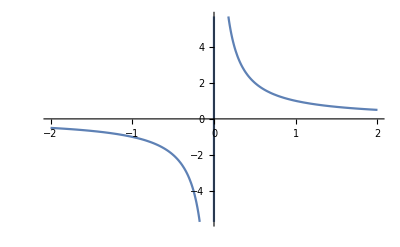

WolframAlphaQueryParseResults

ⅇ^x+ⅇ^x x

WolframAlphaQueryParseResults

1/2 ⅇ^x (Cos[x]+Sin[x])

WolframAlphaQueryParseResults

{{Y[x]→C[1] Cos[x]+C[2] Sin[x]}}

#### Lenguaje de Mathematica: La escritura libre puede ser una buena transición hacía el lenguaje de Mathematica, ya que debajo de cada entrada libre se pueden ver las formas en las que se pueden escribir en el lenguaje. Este lenguaje se sustenta en cuatro reglas básicas las cuales son: Los nombres de las funciones empiezan por mayúsculas, entre corchetes cuadrados [ ] se coloca lo que se quiere evaluar, entre llaves { } las listas o los rangos en los que se quiere evualar y finalmente shift+enter para ejecutar un comandos. Se recomienda el uso de la documentación que ofrece Mathematica para aprender a usar otras funciones y ver cómo es el correcto uso.

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

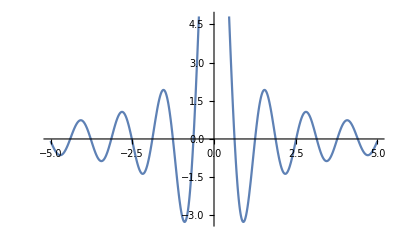

```mathematica
Plot[(3)*Sin[5*x]/x,{x,-5,5}]
```

```mathematica
D[Log[x]*Sin(3*x) - Tanh(x)*Exp[x],x]
```

3 Sin-ⅇ^x Tanh-ⅇ^x Tanh x+3 Sin Log[x]

#### Escritura con paletas: Brindan una estructura sobre la cual se completa la información del cálculo que se quiere realizar. Para acceder a las paletas se puede ir al menú Palettes y luego a la opción Basic Math Assistant.

```mathematica
∫1/(x^2+1)ⅆx
```

ArcTan[x]

```mathematica
∑_(n=1)^∞ 1/n^4
```

π^4/90

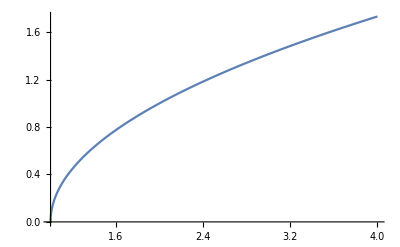

```mathematica
Plot[√(x-1),{x,1,4}]
```

## III. Cálculos básicos

### Operaciones númericas: Mathematica permite realizar cálculos de manera exacta si puede, con lo que es posible tener una gran cantidad de cifras. La respuesta es mostrada lo más reducida posible y tiende a respetar las reglas de cifras significativas. Para aproximar las respuesta a un número dado de cifras significativas se usa la función N[expr, n ] donde n es el número de cifras deseado. Para referirse a una entrada ya realizada se utiliza el signo % seguido del número de la entrada. Lo anterior permite tener un ambiente de trabajo más limpio y mejora los tiempos en la programación. A continuación, se muestran algunas operaciones posibles con Mathematica.

```mathematica
45611565*9561 (*Multiplicación*)
855466/123156 (*División*)
N[855466/123156, 5] (*Aproximación a 5 cifras significativas*)
2^100 (*Exponenciación*)
```

436092172965

427733/61578

6.9462

1267650600228229401496703205376

```mathematica
N[Pi,100] (*Pi con 100 cifras*)
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
N[%122,4] (*Uso de % para referenciación*)
```

3.142

### Funciones Elementales: Mathematica permita trabajar de manera simbólica, así es posible la asignación de expresiones sin la necesidad de delimitar un rango.

#### Polinomios

```mathematica
a=(x+3)^4 (*Polinomio de una variable*)
b= (y+x+z)^6 (*Polinomio en varias variables*)
```

(3+x)^4

(x+y+z)^6

```mathematica
Expand[a] (*Expande la expresión*)
Expand[b]
```

81+108 x+54 x^2+12 x^3+x^4

x^6+6 x^5 y+15 x^4 y^2+20 x^3 y^3+15 x^2 y^4+6 x y^5+y^6+6 x^5 z+30 x^4 y z+60 x^3 y^2 z+60 x^2 y^3 z+30 x y^4 z+6 y^5 z+15 x^4 z^2+60 x^3 y z^2+90 x^2 y^2 z^2+60 x y^3 z^2+15 y^4 z^2+20 x^3 z^3+60 x^2 y z^3+60 x y^2 z^3+20 y^3 z^3+15 x^2 z^4+30 x y z^4+15 y^2 z^4+6 x z^5+6 y z^5+z^6

```mathematica
Exponent[a,x] (*Devuelve el grado del polinomio en x*)
```

4

```mathematica
Collect[b,x] (*Agrupa los términos con la misma potencia de x*)
```

x^6+y^6+6 y^5 z+15 y^4 z^2+20 y^3 z^3+15 y^2 z^4+6 y z^5+z^6+x^5 (6 y+6 z)+x^4 (15 y^2+30 y z+15 z^2)+x^3 (20 y^3+60 y^2 z+60 y z^2+20 z^3)+x^2 (15 y^4+60 y^3 z+90 y^2 z^2+60 y z^3+15 z^4)+x (6 y^5+30 y^4 z+60 y^3 z^2+60 y^2 z^3+30 y z^4+6 z^5)

```mathematica
Factor[x^4-1] (*Factoriza un polinomio*)
Factor[x^4-1,Extension->I](*Factoriza un polinomio en los Complejos*)
Factor[x^4-4,Extension -> {Sqrt[2],I}](*Complejos y permite raíces*)
```

(-1+x) (1+x) (1+x^2)

(-1+x) (-ⅈ+x) (ⅈ+x) (1+x)

-(√2-x) (√2-ⅈ x) (√2+ⅈ x) (√2+x)

```mathematica
(*Los polinomios racionales no son dividos de manera automatica hay que hacerlo explicitamente*)
a=(x^3-y^3) / (x^2-y ^2)
```

(x^3-y^3)/(x^2-y^2)

```mathematica
Cancel[%174] (*Divide el polinomio y simplifica*)
```

(x^2+x y+y^2)/(x+y)

```mathematica
(* La suma de polinomios hay que hacerla explicita*)
c=a+ (x+y)/(4x)
```

(x+y)/(4 x)+(x^3-y^3)/(x^2-y^2)

```mathematica
Together[c] (*Suma de polinomios*)
```

(x^2+4 x^3+2 x y+4 x^2 y+y^2+4 x y^2)/(4 x (x+y))

```mathematica
(*La función clear es usada para limpiar la memoria*)
Clear[a]
Clear[b]
Clear[c]
```

```mathematica
a
```

a

#### Funciones trigonométricas

```mathematica
Sin[Pi/3]
Cos[x] (*Expresión sin evaluar*)
Tan[Pi/6]
```

(√3)/2

Cos[x]

1/(√3)

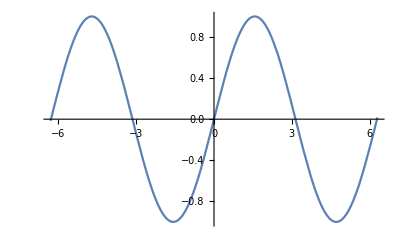

```mathematica
Plot[Sin[x],{x,-6.3,6.3}]
```

```mathematica
(*Expansión de las funciones trigonométricas*)
TrigExpand[Cos[2*x]]
TrigExpand[Sin[x+y]]
```

Cos[x]^2-Sin[x]^2

Cos[y] Sin[x]+Cos[x] Sin[y]

#### Exponenciación, Logaritmos y Potencias

```mathematica
Log[45]
Exp[6]
Sqrt[2]
3^x
```

Log[45]

ⅇ^6

√2

3^x

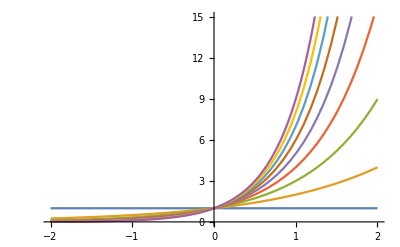

```mathematica
Plot[{1^x,2^x,3^x,4^x,5^x,6^x,7^x,8^x,9^x},{x,-2,2}]
```

### Cálculo: Adicionalmente se cuenta con poderosas herramientas de diferenciación e integración. Usado las funciones Integrate[expr,var] y Derivate[expr,var] (o D[expr,var]) se puede operar la funciones. Es posible también realizar sumatorias y productorias, ya sea usando la paleta disponible o usando los comando Sum[] y Product[].

```mathematica
f=Log[x^5+x+Sin[x]]+Exp[x]/(x+2)
```

ⅇ^x/(2+x)+Log[x+x^5+Sin[x]]

```mathematica
g=D[f,x] (*Derivando*)
```

-ⅇ^x/(2+x)^2+ⅇ^x/(2+x)+(1+5 x^4+Cos[x])/(x+x^5+Sin[x])

```mathematica
Integrate[g,x] (*Integrando la derivada*)
```

ⅇ^x/(2+x)+Log[x+x^5+Sin[x]]

```mathematica
Sum[1/n^4,{n,1,Infinity}]
```

π^4/90

```mathematica
∑_(n=1)^Infinity 1/n^4
```

π^4/90

```mathematica
Product[1+i,{i,1,10}]
```

39916800

### Creando funciones: Mathematica permita crear funciones con el fin de agilizar y tener mejores prácticas en programación. Hemos visto hasta ahora que el signo igual lo podemos usar como asignación, pero si queremos crear funciones debemos usar “:=” . Además, es necesario usar la barra abajo “_” junto al elemento de la función para que se refiera al objeto que entre a la función.

```mathematica
F[x_]:= x^2+x+1
```

```mathematica
(*Evaluando la función creada*)
F[3]
```

13

```mathematica
(*Derivando e integrando la función creada*)
D[F[x],x]
Integrate[F[x],x]
```

1+2 x

x+x^2/2+x^3/3

```mathematica
F[y+10]
Expand[F[y+10]]
F[perro]
```

11+y+(10+y)^2

111+21 y+y^2

1+perro+perro^2

## IV. Graficando

### Gráficos en 2D

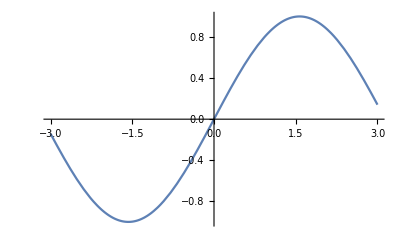

```mathematica
(*El comando más simple para graficar es Plot[expr,{var,min,max}]*)
Plot[ Sin[x],{x,-3,3}]
```

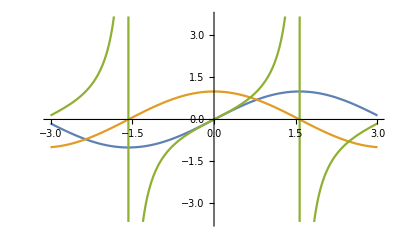

```mathematica
(*Varias gráficas usando el comando Plot*)
Plot[{Sin[x],Cos[x],Tan[x]},{x,-3,3}]
```

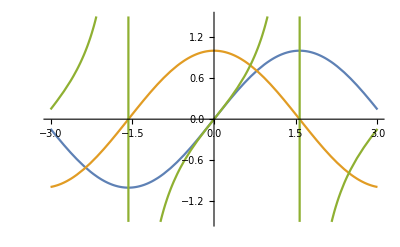

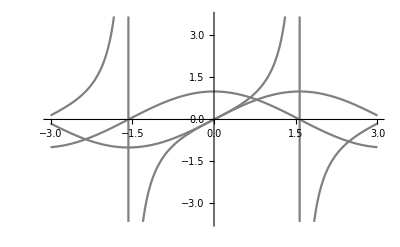

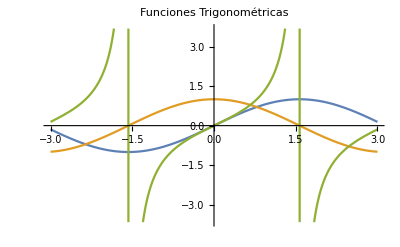

```mathematica
(*Es posible personalizar las gráficas tal que se puedan modificar los rangos en el eje vertical, los estilos,agregar títulos y demás *) 
Plot[{Sin[x],Cos[x],Tan[x]},{x,-3,3}, PlotRange->{-1.5,1.5}]
Plot[{Sin[x],Cos[x],Tan[x]},{x,-3,3}, PlotStyle->Gray]
Plot[{Sin[x],Cos[x],Tan[x]},{x,-3,3}, PlotLabel-> "Funciones Trigonométricas"]
```

#### Curvas Paramétricas

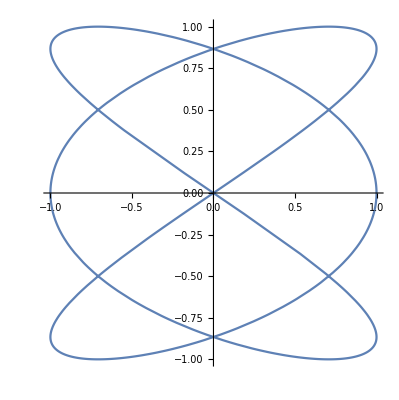

```mathematica
ParametricPlot[{Sin[3*t],Sin[2*t]},{t,0,2*Pi}]
```

#### Campos vectoriales

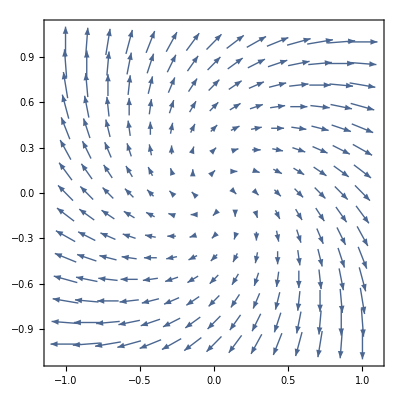

```mathematica
VectorPlot[{y+ x,−x+ y},{x,−1,1},{y,−1,1}]
```

### Gráficos en 3D

```mathematica
T[x_,y_]:=With[{r=Sqrt[x^2+y^2]},Sin[r]/r] 
Plot3D[T[x,y],{x,−10,10},{y,−10,10},PlotRange -> All]
```

-Graphics3D-

## V. Notas Finales

### El estudiante debe reconocer que esta guía es sólo una introducción al bastamente desarrollado mundo de Mathematica, para más información se debe visitar los centros de documentación que posee Mathematica. Finalmente se puede acceder mediante la base de datos de la Universidad a bibliografías especializadas y con los cuales se puede complementar lo aprendido sobre esta herramienta. Bibliografía recomendada: Introduction to Mathematica for Physicists. Andrey Grozin.